```mathematica
(* SPN *)
```

```mathematica
l=4
m=4

sbox="E4D12FB83A6C5907"
IntegerDigits[FromDigits[sbox,16],16,16]
permutation={1,5,9,13,2,6,10,14,3,7,11,15,4,8,12,16}

S[x_]:=IntegerDigits[FromDigits[sbox,16],16,16][[x+1]]

sboxinv=Map[Last,Sort@Map[{S[#],#}&,Range[0,2^l-1]]]
SINV[x_]:=IntegerDigits[FromDigits[sboxinv,16],16,16][[x+1]]

P[x_]:=Map[FromDigits[#,2]&,Partition[Flatten[Map[IntegerDigits[#,2,4]&,x]][[permutation]],4]]
AK[x_,k_]:=MapThread[BitXor,{x,k}]

NR=5
SPNROUND[x_,k_]:=AK[P[S[x]],k]
SPNROUNDINV[x_,k_]:=SINV[P[AK[x,k]]]

Enc[key_,plaintext_]:=Module[{keyschedule,state0,state},
(

keyschedule=Table[RotateLeft[key,i],{i,1,NR+1}];

state0=AK[plaintext,keyschedule[[1]]];
state=Fold[SPNROUND,state0,Drop[Drop[keyschedule,1],-1]];
AK[S[state],keyschedule[[-1]]]
)]

Dec[key_,ciphertext_]:=Module[{keyschedule,dkeys,state0,state},
(

dkeys=Table[RotateLeft[key,i],{i,1,NR+1}];
keyschedule=Reverse@dkeys;

state0=SINV[AK[ciphertext,keyschedule[[1]]]];

state=Fold[SPNROUNDINV,state0,Drop[Drop[keyschedule,1],-1]];
AK[state,keyschedule[[-1]]]
)]
```

4

4

E4D12FB83A6C5907

{14,4,13,1,2,15,11,8,3,10,6,12,5,9,0,7}

{1,5,9,13,2,6,10,14,3,7,11,15,4,8,12,16}

{14,3,4,8,1,12,10,15,7,13,9,6,11,2,0,5}

5

```mathematica
Table[IntegerDigits[S[x],2,4],{x,0,15}]//TableForm
```

1 | 1 | 1 | 0
0 | 1 | 0 | 0
1 | 1 | 0 | 1
0 | 0 | 0 | 1
0 | 0 | 1 | 0
1 | 1 | 1 | 1
1 | 0 | 1 | 1
1 | 0 | 0 | 0
0 | 0 | 1 | 1
1 | 0 | 1 | 0
0 | 1 | 1 | 0
1 | 1 | 0 | 0
0 | 1 | 0 | 1
1 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 1 | 1 | 1

```mathematica
Byte2Nibble[byte_]:={Floor[byte/16],Mod[byte,16]}
(*Byte2Nibble[33]*)

StringToBlocks[message_]:=Partition[Flatten@Map[Byte2Nibble,ToCharacterCode[message]],4];

Nibbles2Byte[pair_]:=pair[[1]]16+pair[[2]]
FromBlocks[blocks_]:=FromCharacterCode@Map[Nibbles2Byte,Partition[Flatten[blocks],2]]
```

```mathematica
(*  Esercizio: riscrivere la SPN con lo stato interno binario a 16 bit *)
```

```mathematica
message="mio messaggio represents an operator form of Fold that can be applied to expressions.";
```

```mathematica
(*
blocks=Partition[Map[FromDigits[#,2]&,Partition[Flatten@Map[IntegerDigits[#,2,8]&,ToCharacterCode[message]],4]],4];
*)

blocks=StringToBlocks[message]
key={1,2,3,4}
ct=Map[Enc[key,#]&,blocks]
pt=Map[Dec[key,#]&,ct]

FromBlocks[blocks]
ciphertext=FromBlocks[ct]
FromBlocks[Map[Dec[key,#]&,ToBlocks[ciphertext]]]
```

{{6,13,6,9},{6,15,2,0},{6,13,6,5},{7,3,7,3},{6,1,6,7},{6,7,6,9},{6,15,2,0},{7,2,6,5},{7,0,7,2},{6,5,7,3},{6,5,6,14},{7,4,7,3},{2,0,6,1},{6,14,2,0},{6,15,7,0},{6,5,7,2},{6,1,7,4},{6,15,7,2},{2,0,6,6},{6,15,7,2},{6,13,2,0},{6,15,6,6},{2,0,4,6},{6,15,6,12},{6,4,2,0},{7,4,6,8},{6,1,7,4},{2,0,6,3},{6,1,6,14},{2,0,6,2},{6,5,2,0},{6,1,7,0},{7,0,6,12},{6,9,6,5},{6,4,2,0},{7,4,6,15},{2,0,6,5},{7,8,7,0},{7,2,6,5},{7,3,7,3},{6,9,6,15},{6,14,7,3}}

{1,2,3,4}

{{8,6,4,14},{4,10,7,10},{3,8,12,1},{8,9,3,4},{14,12,0,8},{2,13,2,10},{4,10,7,10},{0,15,13,5},{15,5,13,5},{10,0,7,3},{15,2,5,12},{5,2,2,15},{3,0,7,2},{8,14,3,9},{8,13,0,2},{5,15,2,7},{4,3,10,0},{14,12,10,8},{1,2,1,12},{14,12,10,8},{3,4,3,2},{9,15,13,8},{9,1,14,3},{13,7,1,6},{10,0,7,6},{4,4,11,1},{4,3,10,0},{10,3,14,0},{9,14,9,10},{9,12,2,2},{4,7,12,5},{0,2,2,8},{10,0,6,12},{10,13,4,3},{10,0,7,6},{1,13,5,10},{14,6,15,7},{1,3,1,14},{0,15,13,5},{8,9,3,4},{10,7,4,3},{9,3,5,12}}

{{6,13,6,9},{6,15,2,0},{6,13,6,5},{7,3,7,3},{6,1,6,7},{6,7,6,9},{6,15,2,0},{7,2,6,5},{7,0,7,2},{6,5,7,3},{6,5,6,14},{7,4,7,3},{2,0,6,1},{6,14,2,0},{6,15,7,0},{6,5,7,2},{6,1,7,4},{6,15,7,2},{2,0,6,6},{6,15,7,2},{6,13,2,0},{6,15,6,6},{2,0,4,6},{6,15,6,12},{6,4,2,0},{7,4,6,8},{6,1,7,4},{2,0,6,3},{6,1,6,14},{2,0,6,2},{6,5,2,0},{6,1,7,0},{7,0,6,12},{6,9,6,5},{6,4,2,0},{7,4,6,15},{2,0,6,5},{7,8,7,0},{7,2,6,5},{7,3,7,3},{6,9,6,15},{6,14,7,3}}

mio messaggio represents an operator form of Fold that can be applied to expressions

.86NJz8Á.894ì\b-*Jz.0fÕõÕ sò\R/0r.8e9.8d.02_'C ì¨.12.1cì¨42.9fØ.91ã×.16 vD±C £à.9e.9a.9c"GÅ.02( lC v.1dZæ÷.13.1e.0fÕ.894§C.93\

MapThread::mptd: Object .86NJz8Á.894ìb-*Jz.0fÕõÕ sò\R/0r.8e9.8d.02_'C ì¨.12.1cì¨42.9fØ.91ã×.16 vD±C £à.9e.9a.9c"GÅ.02( lC v.1dZæ÷.13.1e.0fÕ.894§C.93\ at position {2, 1} in MapThread[BitXor,{.86NJz8Á.894ìb-*Jz.0fÕõÕ sò\R/0r.8e9.8d.02_'C ì¨.12.1cì¨42.9fØ.91ã×.16 vD±C £à.9e.9a.9c"GÅ.02( lC v.1dZæ÷.13.1e.0fÕ.894§C.93\,{3,4,1,2}}] has only 0 of required 1 dimensions.

Part::pkspec1: The expression 1+MapThread[BitXor,{.86NJz8Á.894ìb-*Jz.0fÕõÕ sò\R/0r.8e9.8d.02_'C ì¨.12.1cì¨42.9fØ.91ã×.16 vD±C £à.9e.9a.9c"GÅ.02( lC v.1dZæ÷.13.1e.0fÕ.894§C.93\,{3,4,1,2}}] cannot be used as a part specification.

MapThread::mptd: Object {14,3,4,8,1,12,10,15,7,13,9,6,11,2,0,5}⟦1+MapThread[BitXor,{.86NJz8Á.894ìb-*Jz.0fÕõÕ sò\R/0r.8e9.8d.02_'C ì¨.12.1cì¨42.9fØ.91ã×.16 vD±C £à.9e.9a.9c"GÅ.02( lC v.1dZæ÷.13.1e.0fÕ.894§C.93\,{3,4,1,2}}]⟧ at position {2, 1} in MapThread[BitXor,{{14,3,4,8,1,12,10,15,7,13,9,6,11,2,0,5}⟦1+MapThread[BitXor,{.86NJz8Á.894ìb-*Jz.0fÕõÕ sò\R/0r.8e9.8d.02_'C ì¨.12.1cì¨42.9fØ.91ã×.16 vD±C £à.9e.9a.9c"GÅ.02( lC v.1dZæ÷.13.1e.0fÕ.894§C.93\,{3,4,1,2}}]⟧,{2,3,4,1}}] has only 0 of required 1 dimensions.

MapThread::mptd: Object IntegerDigits[{14,3,4,8,1,12,10,15,7,13,9,6,11,2,0,5}⟦1+MapThread[BitXor,{.86NJz8Á.894ìb-*Jz.0fÕõÕ sò\R/0r.8e9.8d.02_'C ì¨.12.1cì¨42.9fØ.91ã×.16 vD±C £à.9e.9a.9c"GÅ.02( lC v.1dZæ÷.13.1e.0fÕ.894§C.93\,{3,4,1,2}}]⟧,2,4] at position {2, 1} in MapThread[IntegerDigits[BitXor,2,4],{IntegerDigits[{14,3,4,8,1,12,10,15,7,13,9,6,11,2,0,5}⟦1+MapThread[BitXor,{.86NJz8Á.894ìb-*Jz.0fÕõÕ sò\R/0r.8e9.8d.02_'C ì¨.12.1cì¨42.9fØ.91ã×.16 vD±C £à.9e.9a.9c"GÅ.02( lC v.1dZæ÷.13.1e.0fÕ.894§C.93\,{«4»}}]⟧,2,4],{{0,0,1,0},{0,0,1,1},{0,1,0,0},{0,0,0,1}}}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

Part::partw: Part {1,5,9,13,2,6,10,14,3,7,11,15,4,8,12,16} of MapThread[IntegerDigits[BitXor,2,4],{IntegerDigits[{14,3,4,8,1,12,10,15,7,13,9,6,11,2,0,5}⟦1+MapThread[BitXor,{.86NJz8Á.894ìb-*Jz.0fÕõÕ sò\R/0r.8e9.8d.02_'C ì¨.12.1cì¨42.9fØ.91ã×.16 vD±C £à.9e.9a.9c"GÅ.02( lC v.1dZæ÷.13.1e.0fÕ.894§C.93\,{«4»}}]⟧,2,4],{{0,0,1,0},{0,0,1,1},{0,1,0,0},{0,0,0,1}}}] does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::pkspec1: The expression 1+Part[] cannot be used as a part specification.

Part::partw: Part {1,5,9,13,2,6,10,14,3,7,11,15,4,8,12,16} of MapThread[IntegerDigits[BitXor,2,4],{IntegerDigits[{14,3,4,8,1,12,10,15,7,13,9,6,11,2,0,5}⟦1+Part[]⟧,2,4],{{0,0,0,1},{0,0,1,0},{0,0,1,1},{0,1,0,0}}}] does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::pkspec1: The expression 1+Part[] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::partw: Part {1,5,9,13,2,6,10,14,3,7,11,15,4,8,12,16} of MapThread[IntegerDigits[BitXor,2,4],{IntegerDigits[{14,3,4,8,1,12,10,15,7,13,9,6,11,2,0,5}⟦1+Part[]⟧,2,4],{{0,1,0,0},{0,0,0,1},{0,0,1,0},{0,0,1,1}}}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Part::argm will be suppressed during this calculation.

FromCharacterCode::intnm: Non-negative machine-sized integer expected at position 1 in FromCharacterCode[ToBlocks[]].

FromCharacterCode[ToBlocks[]]

```mathematica
NL[alpha_,beta_]:=2^l-Plus@@Table[
								Mod[
									DigitCount[BitAnd[alpha,  input],2,1]+
									DigitCount[BitAnd[ beta ,S[input]],2,1],2],
								{input,0,2^l-1}]
```

```mathematica
tab=Table[NL[alpha,beta],
{alpha,0,2^l-1},
{beta,0,2^l-1}
];
```

1 | 1 | 1 | 0
0 | 1 | 0 | 0
1 | 1 | 0 | 1
0 | 0 | 0 | 1
0 | 0 | 1 | 0
1 | 1 | 1 | 1
1 | 0 | 1 | 1
1 | 0 | 0 | 0
0 | 0 | 1 | 1
1 | 0 | 1 | 0
0 | 1 | 1 | 0
1 | 1 | 0 | 0
0 | 1 | 0 | 1
1 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 1 | 1 | 1

```mathematica
ScalarS[beta_,input_]:=Mod[DigitCount[BitAnd[ beta ,S[input]],2,1],2]
```

```mathematica
Walsh[f_]:=Module[{n,f1,f0,ret},
(
n=Length[f];
Print["input ",f];
If[n==1,Print["base : ",f];f,
{f0,f1}=Partition[f,n/2];Print["f0 : ",f0];Print["f1 : ",f1];
ret=Join[Print["S ",f0+f1];Walsh[f0+f1],Print["D",f0-f1];Walsh[f0-f1]];
Print["walsh: ",ret];
ret
])]
```

```mathematica
f={0,0,1,1,1,0,1,1}



Walsh[f]
```

{0,0,1,1,1,0,1,1}

input {0,0,1,1,1,0,1,1}

f0 : {0,0,1,1}

f1 : {1,0,1,1}

S {1,0,2,2}

input {1,0,2,2}

f0 : {1,0}

f1 : {2,2}

S {3,2}

input {3,2}

f0 : {3}

f1 : {2}

S {5}

input {5}

base : {5}

D{1}

input {1}

base : {1}

walsh: {5,1}

D{-1,-2}

input {-1,-2}

f0 : {-1}

f1 : {-2}

S {-3}

input {-3}

base : {-3}

D{1}

input {1}

base : {1}

walsh: {-3,1}

walsh: {5,1,-3,1}

D{-1,0,0,0}

input {-1,0,0,0}

f0 : {-1,0}

f1 : {0,0}

S {-1,0}

input {-1,0}

f0 : {-1}

f1 : {0}

S {-1}

input {-1}

base : {-1}

D{-1}

input {-1}

base : {-1}

walsh: {-1,-1}

D{-1,0}

input {-1,0}

f0 : {-1}

f1 : {0}

S {-1}

input {-1}

base : {-1}

D{-1}

input {-1}

base : {-1}

walsh: {-1,-1}

walsh: {-1,-1,-1,-1}

walsh: {5,1,-3,1,-1,-1,-1,-1}

{5,1,-3,1,-1,-1,-1,-1}

```mathematica
Walsh[f_]:=Module[{n,f1,f0,ret},
(
	n=Length[f];
	If[n==1,
	f,
		{f0,f1}=Partition[f,n/2];
		Join[Walsh[f0+f1],Walsh[f0-f1]]
	]
)
]
```

```mathematica
AC=Transpose@Table[Walsh[(-1)^Map[ScalarS[b,#]&,Range[0,2^l-1]]],{b,0,2^l-1}];
wLAT=AC/2;
bias=wLAT/2^l//TableForm
```

1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/8 | -1/8 | 0 | 0 | -1/8 | 3/8 | 1/8 | 1/8 | 0 | 0 | 1/8 | 1/8 | 0 | 0
0 | 0 | -1/8 | -1/8 | 0 | 0 | -1/8 | -1/8 | 0 | 0 | 1/8 | 1/8 | 0 | 0 | -3/8 | 1/8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | -3/8 | -1/8 | -1/8 | 1/8 | 1/8 | -1/8 | -1/8
0 | 1/8 | 0 | -1/8 | -1/8 | -1/4 | -1/8 | 0 | 0 | -1/8 | 0 | 1/8 | 1/8 | -1/4 | 1/8 | 0
0 | -1/8 | -1/8 | 0 | -1/8 | 0 | 1/4 | 1/8 | -1/8 | 0 | -1/4 | 1/8 | 0 | -1/8 | -1/8 | 0
0 | 1/8 | -1/8 | 1/4 | 1/8 | 0 | 0 | 1/8 | 0 | -1/8 | 1/8 | 1/4 | -1/8 | 0 | 0 | -1/8
0 | -1/8 | 0 | 1/8 | 1/8 | -1/4 | 1/8 | 0 | -1/8 | 0 | 1/8 | 0 | 1/4 | 1/8 | 0 | 1/8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/8 | 1/8 | 1/8 | -1/8 | 1/8 | -1/8 | -1/8 | -3/8
0 | 0 | -1/8 | -1/8 | 0 | 0 | -1/8 | -1/8 | -1/4 | 0 | -1/8 | 1/8 | 0 | 1/4 | 1/8 | -1/8
0 | 1/4 | -1/8 | 1/8 | -1/4 | 0 | 1/8 | -1/8 | 1/8 | 1/8 | 0 | 0 | 1/8 | 1/8 | 0 | 0
0 | 1/4 | 0 | -1/4 | 1/4 | 0 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/8 | 1/4 | -1/8 | -1/8 | 0 | 1/8 | 0 | 1/8 | 0 | 1/8 | 1/4 | 0 | 1/8 | 0 | -1/8
0 | 1/8 | 1/8 | 0 | -1/8 | 1/4 | 0 | 1/8 | -1/4 | -1/8 | 1/8 | 0 | 1/8 | 0 | 0 | 1/8
0 | 1/8 | 1/8 | 0 | -1/8 | -1/4 | 0 | 1/8 | -1/8 | 0 | 0 | -1/8 | -1/4 | 1/8 | -1/8 | 0
0 | -1/8 | -1/4 | -1/8 | -1/8 | 0 | 1/8 | 0 | 0 | -1/8 | 1/4 | -1/8 | -1/8 | 0 | 1/8 | 0

1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/8 | -1/8 | 0 | 0 | -1/8 | 3/8 | 1/8 | 1/8 | 0 | 0 | 1/8 | 1/8 | 0 | 0
0 | 0 | -1/8 | -1/8 | 0 | 0 | -1/8 | -1/8 | 0 | 0 | 1/8 | 1/8 | 0 | 0 | -3/8 | 1/8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | -3/8 | -1/8 | -1/8 | 1/8 | 1/8 | -1/8 | -1/8
0 | 1/8 | 0 | -1/8 | -1/8 | -1/4 | -1/8 | 0 | 0 | -1/8 | 0 | 1/8 | 1/8 | -1/4 | 1/8 | 0
0 | -1/8 | -1/8 | 0 | -1/8 | 0 | 1/4 | 1/8 | -1/8 | 0 | -1/4 | 1/8 | 0 | -1/8 | -1/8 | 0
0 | 1/8 | -1/8 | 1/4 | 1/8 | 0 | 0 | 1/8 | 0 | -1/8 | 1/8 | 1/4 | -1/8 | 0 | 0 | -1/8
0 | -1/8 | 0 | 1/8 | 1/8 | -1/4 | 1/8 | 0 | -1/8 | 0 | 1/8 | 0 | 1/4 | 1/8 | 0 | 1/8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/8 | 1/8 | 1/8 | -1/8 | 1/8 | -1/8 | -1/8 | -3/8
0 | 0 | -1/8 | -1/8 | 0 | 0 | -1/8 | -1/8 | -1/4 | 0 | -1/8 | 1/8 | 0 | 1/4 | 1/8 | -1/8
0 | 1/4 | -1/8 | 1/8 | -1/4 | 0 | 1/8 | -1/8 | 1/8 | 1/8 | 0 | 0 | 1/8 | 1/8 | 0 | 0
0 | 1/4 | 0 | -1/4 | 1/4 | 0 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/8 | 1/4 | -1/8 | -1/8 | 0 | 1/8 | 0 | 1/8 | 0 | 1/8 | 1/4 | 0 | 1/8 | 0 | -1/8
0 | 1/8 | 1/8 | 0 | -1/8 | 1/4 | 0 | 1/8 | -1/4 | -1/8 | 1/8 | 0 | 1/8 | 0 | 0 | 1/8
0 | 1/8 | 1/8 | 0 | -1/8 | -1/4 | 0 | 1/8 | -1/8 | 0 | 0 | -1/8 | -1/4 | 1/8 | -1/8 | 0
0 | -1/8 | -1/4 | -1/8 | -1/8 | 0 | 1/8 | 0 | 0 | -1/8 | 1/4 | -1/8 | -1/8 | 0 | 1/8 | 0

```mathematica
LAT =tab-8;



LAT//TableForm
```

8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 | -2 | 0 | 0 | -2 | 6 | 2 | 2 | 0 | 0 | 2 | 2 | 0 | 0
0 | 0 | -2 | -2 | 0 | 0 | -2 | -2 | 0 | 0 | 2 | 2 | 0 | 0 | -6 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | -6 | -2 | -2 | 2 | 2 | -2 | -2
0 | 2 | 0 | -2 | -2 | -4 | -2 | 0 | 0 | -2 | 0 | 2 | 2 | -4 | 2 | 0
0 | -2 | -2 | 0 | -2 | 0 | 4 | 2 | -2 | 0 | -4 | 2 | 0 | -2 | -2 | 0
0 | 2 | -2 | 4 | 2 | 0 | 0 | 2 | 0 | -2 | 2 | 4 | -2 | 0 | 0 | -2
0 | -2 | 0 | 2 | 2 | -4 | 2 | 0 | -2 | 0 | 2 | 0 | 4 | 2 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 2 | 2 | -2 | 2 | -2 | -2 | -6
0 | 0 | -2 | -2 | 0 | 0 | -2 | -2 | -4 | 0 | -2 | 2 | 0 | 4 | 2 | -2
0 | 4 | -2 | 2 | -4 | 0 | 2 | -2 | 2 | 2 | 0 | 0 | 2 | 2 | 0 | 0
0 | 4 | 0 | -4 | 4 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -2 | 4 | -2 | -2 | 0 | 2 | 0 | 2 | 0 | 2 | 4 | 0 | 2 | 0 | -2
0 | 2 | 2 | 0 | -2 | 4 | 0 | 2 | -4 | -2 | 2 | 0 | 2 | 0 | 0 | 2
0 | 2 | 2 | 0 | -2 | -4 | 0 | 2 | -2 | 0 | 0 | -2 | -4 | 2 | -2 | 0
0 | -2 | -4 | -2 | -2 | 0 | 2 | 0 | 0 | -2 | 4 | -2 | -2 | 0 | 2 | 0

```mathematica
wLAT==LAT
```

True

0 | 2 | 2 | 0 | 0 | 2 | 6 | 2 | 2 | 0 | 0 | 2 | 2 | 0 | 0
0 | 2 | 2 | 0 | 0 | 2 | 2 | 0 | 0 | 2 | 2 | 0 | 0 | 6 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 6 | 2 | 2 | 2 | 2 | 2 | 2
2 | 0 | 2 | 2 | 4 | 2 | 0 | 0 | 2 | 0 | 2 | 2 | 4 | 2 | 0
2 | 2 | 0 | 2 | 0 | 4 | 2 | 2 | 0 | 4 | 2 | 0 | 2 | 2 | 0
2 | 2 | 4 | 2 | 0 | 0 | 2 | 0 | 2 | 2 | 4 | 2 | 0 | 0 | 2
2 | 0 | 2 | 2 | 4 | 2 | 0 | 2 | 0 | 2 | 0 | 4 | 2 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 6
0 | 2 | 2 | 0 | 0 | 2 | 2 | 4 | 0 | 2 | 2 | 0 | 4 | 2 | 2
4 | 2 | 2 | 4 | 0 | 2 | 2 | 2 | 2 | 0 | 0 | 2 | 2 | 0 | 0
4 | 0 | 4 | 4 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 4 | 2 | 2 | 0 | 2 | 0 | 2 | 0 | 2 | 4 | 0 | 2 | 0 | 2
2 | 2 | 0 | 2 | 4 | 0 | 2 | 4 | 2 | 2 | 0 | 2 | 0 | 0 | 2
2 | 2 | 0 | 2 | 4 | 0 | 2 | 2 | 0 | 0 | 2 | 4 | 2 | 2 | 0
2 | 4 | 2 | 2 | 0 | 2 | 0 | 0 | 2 | 4 | 2 | 2 | 0 | 2 | 0

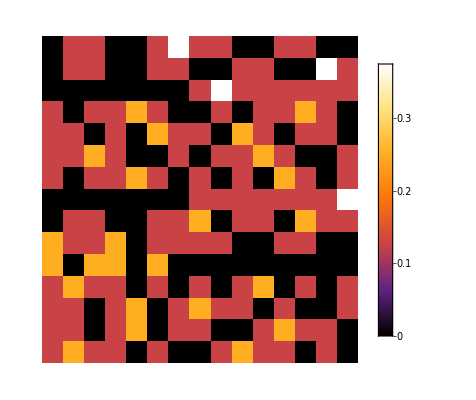

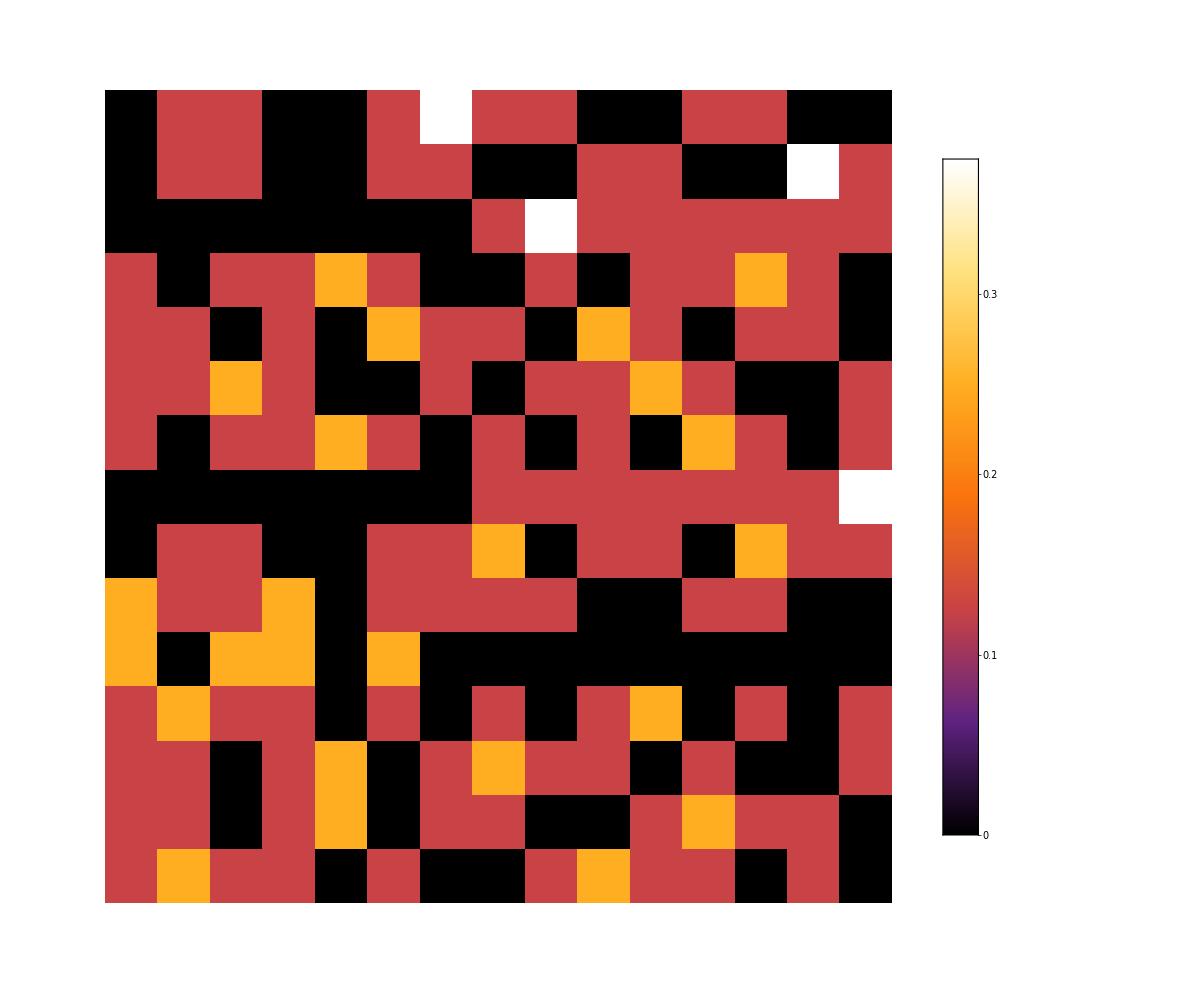

```mathematica
bias=Abs[wLAT];

(* elimino la prima riga e la prima colonna della LAT*)
reducedbias=Map[Drop[#,1]&,Drop[bias,1]];
TableForm[reducedbias]
ArrayPlot[reducedbias,ColorFunction->"SunsetColors",
PlotLegends->BarLegend[{"SunsetColors",{0,3/8}}]]
```

```mathematica
HammingDistance[IntegerDigits[3,2],Table[0,2]]
```

2

```mathematica
Mod[DigitCount[7,2,1],2]
```

```mathematica
SPNROUND[{2,5,6,1},{16,15,16,11}]
```

```mathematica
P[S[{2,5,6,1}]]
AK[{14,13,6,14},{16,15,16,11}]
```

```mathematica
BitXor[14,16]
```

```mathematica
?Fold
```

```mathematica
Nest[f,x,3]
```

```mathematica
?Round
```

```mathematica
P[S[x]]
```

```mathematica
P[S[x]]
```

```mathematica
Table[A[i],{i,1,16}][[permutation]]
```

{A[1],A[5],A[9],A[13],A[2],A[6],A[10],A[14],A[3],A[7],A[11],A[15],A[4],A[8],A[12],A[16]}

```mathematica
Node[sboxindex_,alpha_]
```

```mathematica
ClearAll[MakeBias]
```

```mathematica
tab
```

```mathematica
tab=Table[NL[alpha,beta],{alpha,0,2^l-1},{beta,0,2^l-1}];
bias=Abs[(tab-2^(l-1))/16];
MakeBias[node_]:=Module[
{alpha,weights},
alpha=nodes[[node,2]];
weights=DigitCount[Range[0,15],2,1];
row=bias[[alpha+1]];
(*Print[row];*)
(*Print@TableForm[Transpose@{Range[0,15],weights,bias[[alpha+1]]}];*)
Select[Transpose@{Range[0,15],weights,bias[[alpha+1]]},(#[[2]]==1)&&(#[[3]]>0)&]
]
```

```mathematica
ToBlock[index_,beta_]:=Module[{out},out={0,0,0,0};out[[index+1]]=beta;out]
FromBlock[block_]:=Module[{out},
Map[{#-1,block[[#]]}&  ,Flatten@Position[block,_?(#>0&)]]
]

MakeEdgesFromNode[node_]:=
Module[{},
(
nblock=node[[1]];
alpha=node[[2]];
anybias=MakeBias[alpha+1];

Map[(beta=#[[1]];out={0,0,0,0};out[[nblock+1]]=beta;
{node->FromBlock[P[out]][[1]],#[[3]]})&,anybias]
)]
```

```mathematica
Map[MakeEdgesFromNode,FromBlock[{3,0,0,0}]]
```

{{{{0,3}→{0,8},1/8}}}

```mathematica
PositiveIntegers[2]
```

```mathematica
ToBlock[1,3]
```

```mathematica
(* set of starting nodes - una s-box attiva *)
nodes=Flatten[Table[{index,alpha},{index,0,3},{alpha,0,2^l-1}],1]


(* generiamo tutti gli archi che partono dai nodi *) 
i=2
edges=Flatten[Map[MakeEdgesFromNode,nodes],1];

TableForm[scc=ConnectedComponents[G=Graph[Map[First,edges],VertexLabels->"Name",EdgeLabels->Map[Last,edges]]],TableDepth->1];
```

{{0,0},{0,1},{0,2},{0,3},{0,4},{0,5},{0,6},{0,7},{0,8},{0,9},{0,10},{0,11},{0,12},{0,13},{0,14},{0,15},{1,0},{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,11},{1,12},{1,13},{1,14},{1,15},{2,0},{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{2,11},{2,12},{2,13},{2,14},{2,15},{3,0},{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{3,11},{3,12},{3,13},{3,14},{3,15}}

2

```mathematica
Position[nodes,{2,8}]
MakeBias[41]
Position[nodes,{0,2}]
MakeBias[3]
```

```mathematica
(*TableForm[scc,TableDepth->1]*)
TableForm[Select[scc,Length[#]>1&],TableDepth->1]
CommunityGraphPlot@G
```

{{2,8},{0,2}}
{{0,4},{1,8}}
{{2,4},{1,2}}

-Graphics-

```mathematica
Graph[G]
```

```mathematica
TableForm@Map[#->MakeBias[#]&,Range[2,15]]
```

```mathematica
row
```

```mathematica
weights=DigitCount[Range[0,15],2,1];
Transpose@{Range[0,15],weights,bias[[alpha+1]]}
```

```mathematica
MakeBias[2]
```

```mathematica
N@(3/8)^4
N@(1/8)
```

```mathematica
epsilon=1/32 1/32 2
1/epsilon^2

2^16
```

```mathematica
FindCycle[G,Infinity,All]
```

{{{2,4}->{1,2},{1,2}->{2,4}},{{0,4}->{1,8},{1,8}->{0,4}},{{2,8}->{0,2},{0,2}->{2,8}}}

```mathematica
LayeredGraphPlot@G
```